```mathematica
fMS[kappa_,theta_,c_]:=Exp[kappa*Cos[theta]^2]/(c)
```

```mathematica
Integrate[fMS[kappa,theta],{theta,0,Pi/2}]/(Pi/2)
```

(ⅇ^(kappa/2) BesselI[0,kappa/2])/c

```mathematica
Integrate[fMS[kappa,theta]*Sin[theta],{theta,0,Pi/2}]
```

(√π Erfi[√kappa])/(2 c √kappa)

```mathematica
fONSAGER[kappa_,theta_]:=Cosh[kappa*Cos[theta]]/(Sinh[kappa]/kappa)
```

```mathematica
Integrate[fONSAGER[kappa,theta]*Sin[theta],{theta,0,Pi/2}]
```

1

```mathematica
IMS[kappa_,psi_]:=Integrate[fMS[kappa,theta]*Sin[theta]/(Cos[psi]^2*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2},Assumptions->psi>0 && psi<Pi/2]
```

```mathematica
IMS[kappa,psi]
```

```mathematica
(ⅇ^(kappa Cos[psi]^2) √π Erf[√kappa Cos[psi]] Sec[psi])/(2 c √kappa)
```

```mathematica
Integrate[(ⅇ^(kappa Cos[psi]^2) √π Erf[√kappa Cos[psi]] Sec[psi])/(2 c √kappa),{psi,0,Pi/2}]/(Pi/2)
```

(2 ∫_0^(π/2) (ⅇ^(kappa Cos[psi]^2) √π Erf[√kappa Cos[psi]] Sec[psi])/(2 c √kappa)ⅆpsi)/π

```mathematica
IONSAGER[kappa_,psi_]:=Integrate[fONSAGER[kappa,theta]*Sin[theta]/(Cos[psi]^2*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2},Assumptions->psi>0 && psi<Pi/2]
```

```mathematica
IONSAGER[kappa,psi]
```

Integrate[(Cosh[kappa Cos[theta]] Sec[psi]^2 Sin[theta])/(√(-Tan[psi]^2+Tan[theta]^2)),{theta,psi,π/2},Assumptions→psi≥0&&psi≤π/2]

```mathematica
IMScorr[kappa_,psi_]:=Integrate[fMS[kappa,theta]*Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2},Assumptions->psi>0 && psi<Pi/2]
```

```mathematica
IMScorr[kappa,psi]
```

```mathematica
Integrate[(ⅇ^(kappa Cos[theta]^2))/c*Sin[theta]/Sqrt[Cos[psi]^2-Cos[theta]^2],{theta,psi,π/2},Assumptions->psi>0&&psi<π/2]
```

Integrate[(ⅇ^(kappa Cos[theta]^2) Sin[theta])/(c √(Cos[psi]^2-Cos[theta]^2)),{theta,psi,π/2},Assumptions→psi>0&&psi<π/2]

```mathematica
Limit[IMScorr[kappa,psi],psi->Pi/2,Direction->1]
```

π/(2 c)

```mathematica
FullSimplify[fMS[kappa,0]/(Pi/2/c)]
```

(2 ⅇ^kappa)/π

```mathematica
Rat[theta_,psi_]:=Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2])/(Sin[theta]/Sqrt[Cos[psi]^2-Cos[theta]^2])
```

```mathematica
Plot3D[Rat[theta, psi],{theta,0,Pi/2},{psi,0,Pi/2}]
```

-Graphics3D-

```mathematica
IMK[kappa_,theta_,psi_]:=fMS[kappa,theta]*Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2])
```

```mathematica
Series[IMK[kappa,theta,psi],{theta,psi,0}]
```

(ⅇ^(kappa Cos[psi]^2) √kappa √(2/π) Sec[psi] Tan[psi])/(Erfi[√kappa] √(-(psi-theta) (Tan[psi]+Tan[psi]^3)))+O[theta-psi]^1

```mathematica
Limit[IMK[kappa,theta,psi],psi->Pi/2]
```

(2 ⅈ ⅇ^(kappa Cos[theta]^2) √kappa Tan[theta])/(√π Erfi[√kappa])

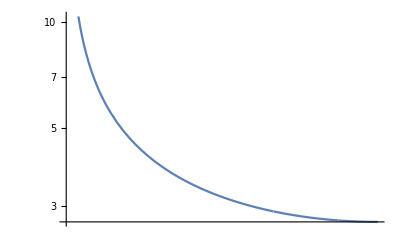

```mathematica
LogLogPlot[IMK[2,theta,0.9*Pi/2],{theta,0.9*Pi/2,Pi/2}]
```

```mathematica
IMScorr[kappa,psi]
```

∫_psi^(π/2) (fMS[kappa,theta] Sec[psi] Tan[theta])/(√(-Tan[psi]^2+Tan[theta]^2))ⅆtheta

```mathematica
IONSAGERcorr[kappa_,psi_]:=Integrate[fONSAGER[kappa,theta]*Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

```mathematica
IONSAGERcorr[kappa,psi]
```

∫_psi^(π/2) (Cosh[kappa Cos[theta]] Sec[psi] Tan[theta])/(√(-Tan[psi]^2+Tan[theta]^2))ⅆtheta

```mathematica
NIMS[kappa_,psi_]:=NIntegrate[fMS[kappa,theta]*Sin[theta]/(Cos[psi]^2*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

```mathematica
NIONSAGER[kappa_,psi_]:=NIntegrate[fONSAGER[kappa,theta]*Sin[theta]/(Cos[psi]^2*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

```mathematica
NIMScorr[kappa_,psi_,c_]:=NIntegrate[fMS[kappa,theta,c]*Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

```mathematica
IMSanal[kappa_,psi_]:=1/8*Exp[kappa*Cos[psi]^2/2]*BesselI[0,kappa*Cos[psi]^2/2] * Sqrt[kappa]/(Exp[kappa]*DawsonF[Sqrt[kappa]])
```

```mathematica
IMSanal[kappa,psi]
```

(ⅇ^(-kappa+1/2 kappa Cos[psi]^2) √kappa BesselI[0,1/2 kappa Cos[psi]^2])/(8 DawsonF[√kappa])

```mathematica
Series[Integrate[IMSanal[kappa,psi],{psi,0,Pi/2}]/(Pi/2),{kappa,Infinity}]
```

Series[(2 ∫_0^(π/2) (ⅇ^(-kappa+1/2 kappa Cos[psi]^2) √kappa BesselI[0,1/2 kappa Cos[psi]^2])/(8 DawsonF[√kappa])ⅆpsi)/π,{kappa,∞}]

```mathematica
LogLogPlot[NIntegrate[IMSanal[-kappa,psi],{psi,0,Pi/2}]/(Pi/2),{kappa,,1000}]
```

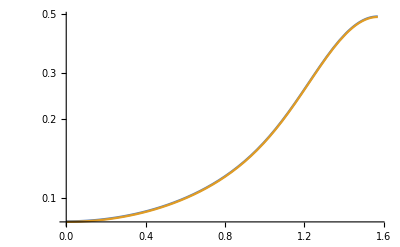

```mathematica
LogPlot[{Abs[NIMScorr[-12,psi,3.2]],IMSanal[-12,psi]},{psi,0,Pi/2},PlotRange->All]
```

```mathematica
NIONSAGERcorr[kappa_,psi_]:=NIntegrate[fONSAGER[kappa,theta]*Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
NONSAGERcorr[kappa_]:= NIntegrate[NIONSAGERcorr[kappa,psi],{psi,0,Pi/2}]
```

```mathematica
NMS[kappa_]:= NIntegrate[NIMS[kappa,psi],{psi,0,Pi/2}]
```

```mathematica
NMScorr[kappa_]:= NIntegrate[NIMScorr[kappa,psi],{psi,0,Pi/2}]
```

```mathematica
NONSAGER[kappa_]:= NIntegrate[NIONSAGER[kappa,psi],{psi,0,Pi/2}]
```

```mathematica
NONSAGERcorr[-3]*2/Pi
```

NIntegrate::nlim: theta = psi is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.27558

```mathematica
NMScorr[2]*2/Pi
```

NIntegrate::nlim: theta = psi is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.31764

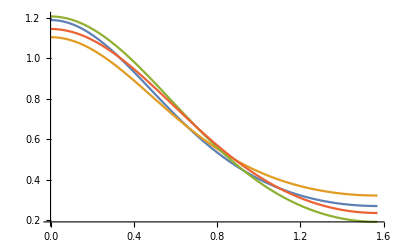

```mathematica
Plot[{NIMS[2,psi]/(Pi/2),NIMScorr[2,psi]/(Pi/2*1.317),1*NIONSAGER[-3,psi]/(Pi/2),1*NIONSAGERcorr[-3,psi]/(Pi/2*1.27558)},{psi,0,Pi/2}]
```

```mathematica
fSHRINK[lambda_,theta_]:=1/2*lambda^2*Cos[ArcTan[lambda*Tan[theta]]]^3/Cos[theta]^3
```

```mathematica
Quarter[theta_]:=Piecewise[{{Abs[theta]-Floor[Abs[theta],Pi],(Abs[theta]-Floor[Abs[theta],Pi])<=Pi/2},{Pi-(Abs[theta]-Floor[Abs[theta],Pi]),(Abs[theta]-Floor[Abs[theta],Pi])>Pi/2}}]
```

```mathematica
Floor[4,Pi]
```

π

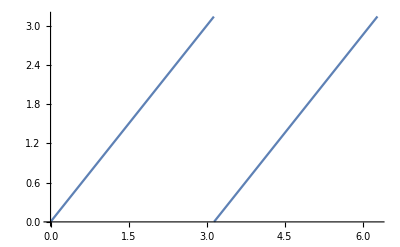

```mathematica
Plot[Abs[theta]-Floor[Abs[theta],Pi],{theta,0,2*Pi}]
```

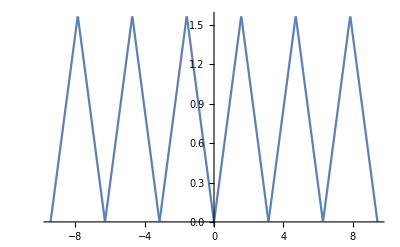

```mathematica
Plot[Quarter[theta],{theta,-3*Pi,3*Pi}]
```

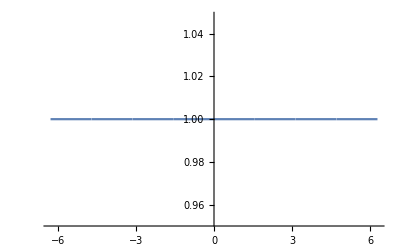

```mathematica
Plot[2*fSHRINK[1,Quarter[theta]],{theta,-2*Pi,2*Pi}]
```

```mathematica
p[theta_,lambda_]:=
```

```mathematica
FullSimplify[2*fSHRINK[kappa,psi]]
```

(kappa^2 Sec[psi]^3)/((1+kappa^2 Tan[psi]^2)^(3/2))

```mathematica
Limit[(kappa^2 Sec[psi]^3)/((1+kappa^2 Tan[psi]^2)^(3/2)),psi->Pi/2,Assumptions->kappa>0]
```

-1/kappa

```mathematica
FullSimplify[Normal[Series[(kappa^2 Sec[psi]^3)/((1+kappa^2 Tan[psi]^2)^(3/2)),{psi,Pi/2,0}]]]
```

(kappa^2 (8+3 (π-2 psi)^2)-3 (π-2 psi)^2)/(8 (kappa^2/(π-2 psi)^2)^(3/2) (π-2 psi)^3)